```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Graeme\Dropbox\coding\ML_dft

```mathematica
inp=Flatten[Import["train_data/energies.dat","Table"]];
pred=Flatten[Import["predict_data/predicted_energies.dat","Table"]];
```

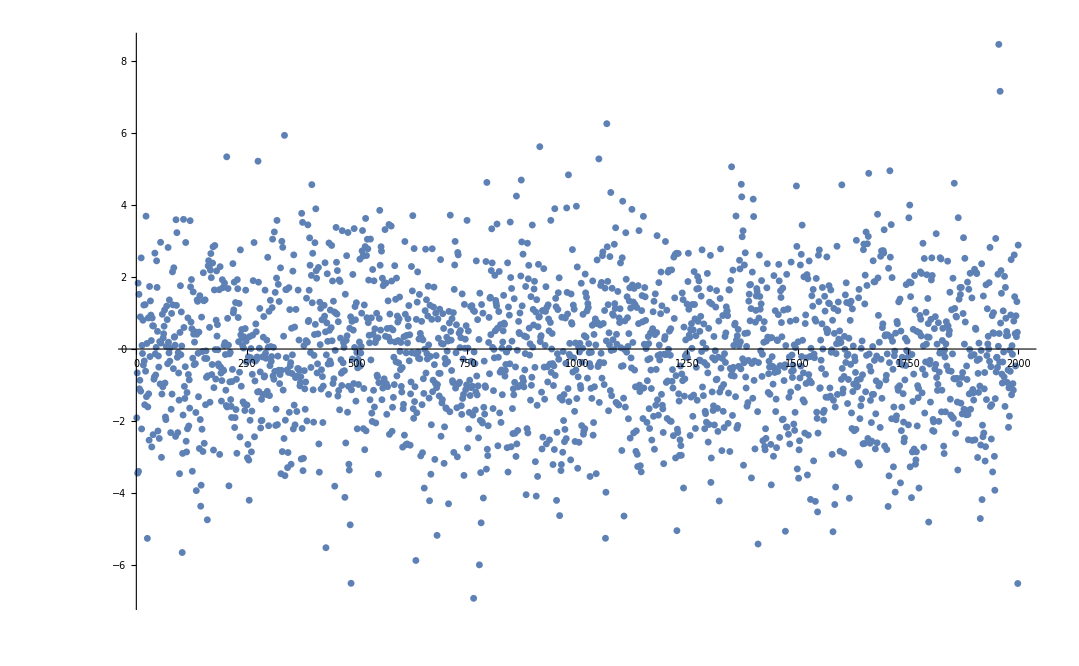

```mathematica
ListPlot[{inp-pred}]
```

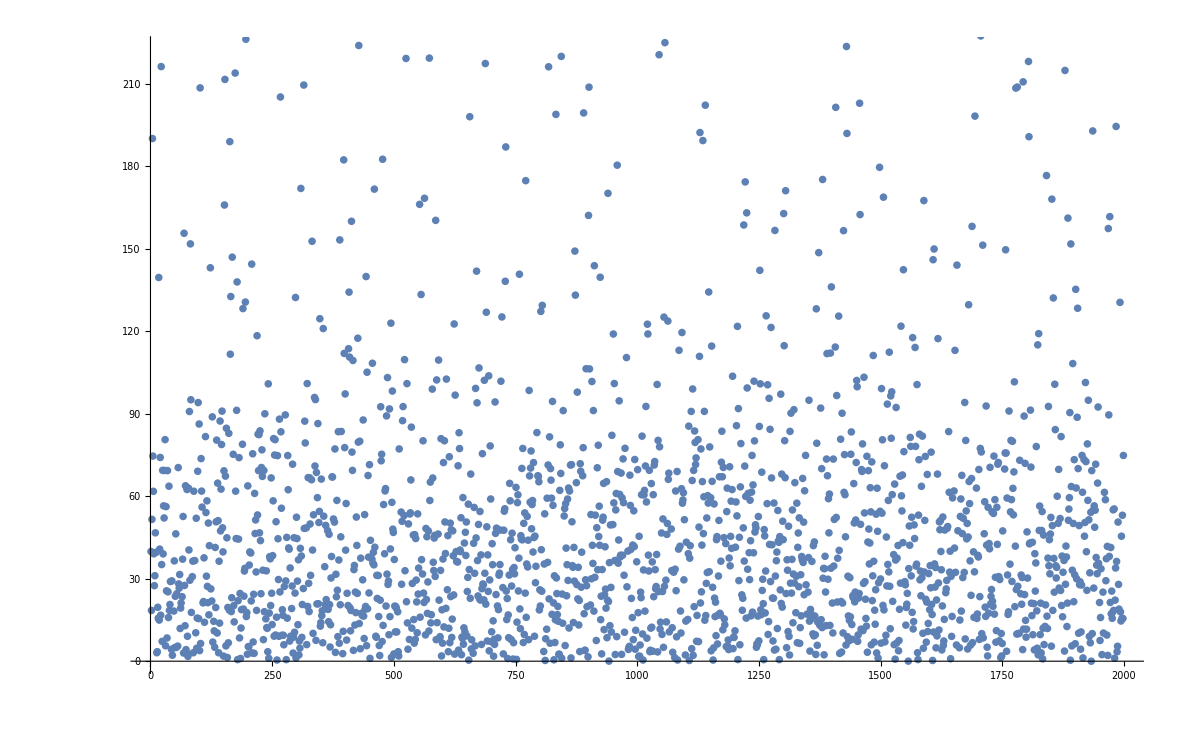

```mathematica
ListPlot[{100Abs@((inp-pred)/inp)}]
```